# Mathematica Supplement B: SEIRS model with Alternative Matching Alleles Model

Joint coevolutionary-epidemiological models dampen Red Queen cycles and alter conditions for epidemics, Ailene MacPherson and Sarah P. Otto, Theoretical Population Biology.

## Alternative to Matching Alleles Model

```mathematica
Clear["Global`*"];
```

Here we derive a model similar to the classic single locus matching alleles model except where after infection pathogens must progress from a juvenile to mature state before the host becomes infectious. Using equilibrium stability analysis we show that including pathogen maturation can produce limit cycles in allele frequencies.

### The Differential Equations

#### The Host Equation

Let ρ[i,t] be the probability that a host of type i is infected in the small unit of time from t to t+Δt

```mathematica
ρ[i_,t_]:=Δt(β[i,1]pM[t]+β[i,2](1-pM[t]));
```

Here β[i,j] is the probability that a host of type i is infected by a pathogen of type j and where pM[t] is the frequency of mature type 1 pathogens.  
The resulting fitness of type i host is:

```mathematica
WH[i_,t_]:=1-ξH ρ[i,t]
```

Here ξH is the fitness cost of infection.  The frequency of type 1 hosts (pH) at time t+Δt is therefore given by:

```mathematica
pH[t+Δt]=(pH[t]WH[1,t])/(pH[t]WH[1,t]+(1-pH[t])WH[2,t])//Simplify
```

(pH[t] (-1+Δt ξH pM[t] (β[1,1]-β[1,2])+Δt ξH β[1,2]))/(-1+Δt ξH pM[t] (β[2,1]-β[2,2])+Δt ξH β[2,2]+Δt ξH pH[t] (β[1,2]-β[2,2]+pM[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2])))

Using the definition of a derivative

```mathematica
Limit[(pH[t+Δt]-pH[t])/Δt,Δt->0]//Simplify
```

ξH (-1+pH[t]) pH[t] (β[1,2]-β[2,2]+pM[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2]))

Letting d/dt pH[t]=f1[t] and rewriting the above expression

```mathematica
f1[t_]:=-ξH (1-pH[t]) pH[t] ((β[1,1]-β[2,1])pM[t]+(β[1,2]-β[2,2])(1-pM[t]))
```

#### The Immature Pathogen Equation

The probability that a mature pathogen of type i infects a host is given by:

```mathematica
η[i_,t_]:=Δt(β[1,i]pH[t]+β[2,i](1-pH[t]));
```

If infection increases a pathogens fitness by a benefit ξP then pathogen fitness is given by the following.

```mathematica
WP[i_,t_]:=1+ξP η[i,t]
```

The frequency of type 1 immature pathogens after infection (selection) is given by:

```mathematica
pP[t+Δt]=pP[t](1-γ)+γ(pM[t]WP[1,t])/(pM[t]WP[1,t]+(1-pM[t])WP[2,t])
```

(1-γ) pP[t]+(γ pM[t] (1+Δt ξP (pH[t] β[1,1]+(1-pH[t]) β[2,1])))/(pM[t] (1+Δt ξP (pH[t] β[1,1]+(1-pH[t]) β[2,1]))+(1-pM[t]) (1+Δt ξP (pH[t] β[1,2]+(1-pH[t]) β[2,2])))

Assuming that mature pathogens are quickly replaced by immature pathogens pP[t]≈pM[t].  Using the definition of the derivative

```mathematica
Collect[Limit[(pP[t+Δt]-(1-γ)pP[t]-γ pM[t])/Δt,Δt->0],μ,Simplify]
```

-γ ξP (-1+pM[t]) pM[t] (β[2,1]-β[2,2]+pH[t] (β[1,1]-β[1,2]-β[2,1]+β[2,2]))

Letting f2[t]≈d/dt pP[t] and rewriting the above expression we have the approximate expression for the change in the frequency of immature pathogens.

```mathematica
f2[t_]:=γ ξP (1-pM[t]) pM[t] (pH[t] (β[1,1]-β[1,2])+(1-pH[t])(β[2,1]-β[2,2]));
```

In addition to changes due to fitness the pathogens mutate type at rate μ, the net effect of the frequency of type 1 pathogens is given by  μ(1-pP[t])-μ pP[t]=(1-2pP[t])μ

```mathematica
f2[t_]:=γ ξP (1-pM[t]) pM[t] (pH[t] (β[1,1]-β[1,2])+(1-pH[t])(β[2,1]-β[2,2]))+(1-2pP[t])μ
```

If pP[t] and pM[t] are not linked closely enough f2[t] may be positive (negative) when pP[t]=1 (pP[t]=0) causing the allele frequency to exceed the biological range of an allele frequency.

#### The Mature Pathogen Equation

Each generation suppose a fraction γ of the mature pathogen population is removed and replace with individuals from the immature pathogen class.  The above assumption that pP[t]≈pM[t] implies that γ is large.  In addition suppose mature pathogens mutate at a rate μ. The resulting frequency of mature pathogens at time t+Δt is given by the following.

```mathematica
pM[t+Δt]=(1-γ Δt)pM[t]+γ Δt pP[t]//Simplify;
```

Using the definition of the derivative

```mathematica
Limit[(pM[t+Δt]-pM[t])/Δt,Δt->0]
```

γ (-pM[t]+pP[t])

Letting f3[t]=d/dt pM[t]

```mathematica
f3[t_]:=γ pP[t]-γ pM[t]
```

#### The system of Equations

To simplify the analysis of this system we assume that the infection matrix β is symmetric such that infection of like types (unlike types) occur at the same rates, this implies that β[1,1]=β[2,2]=X, and β[1,2]=β[2,1]=Y. We assume that X>Y.

```mathematica
βsub={β[1,1]->X,β[1,2]->Y,β[2,1]->Y,β[2,2]->X};
```

The resulting system of ordinary differential equations describing the change in allele frequency is

```mathematica
ODE[t_]:={D[pH[t],t]== f1[t],D[pP[t],t]== f2[t],D[pM[t],t]== f3[t]}/.βsub;
```

The list of variables is given by

```mathematica
Vars[t_]:={pH[t],pP[t],pM[t]};
```

```mathematica
ODE[t]
```

{pH'[t]==-ξH (1-pH[t]) pH[t] ((-X+Y) (1-pM[t])+(X-Y) pM[t]),pP'[t]==ξP ((-X+Y) (1-pH[t])+(X-Y) pH[t]) (1-pM[t]) pM[t]+μ (1-2 pP[t]),pM'[t]==-γ pM[t]+γ pP[t]}

### The Equilibria

```mathematica
EquiEqus={f1[t]==0,f2[t]==0,f3[t]==0}/.βsub
```

{-ξH (1-pH[t]) pH[t] ((-X+Y) (1-pM[t])+(X-Y) pM[t])==0,ξP ((-X+Y) (1-pH[t])+(X-Y) pH[t]) (1-pM[t]) pM[t]+μ (1-2 pP[t])==0,-γ pM[t]+γ pP[t]==0}

```mathematica
equilibria=Solve[EquiEqus,Vars[t]]//FullSimplify
```

{{pH[t]→1/2,pP[t]→1/2,pM[t]→1/2},{pH[t]→1,pP[t]→-(2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→-(2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)},{pH[t]→1,pP[t]→(-2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→(-2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)},{pH[t]→0,pP[t]→(2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→(2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)},{pH[t]→0,pP[t]→-(-2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→-(-2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)}}

The polymorphic equilibrium is given by {pH[t]→1/2,pP[t]→1/2,pM[t]→1/2}.  The rest of the equilibria are points near fixation as can be seen by setting μ=0

```mathematica
Solve[EquiEqus/.βsub/.μ->0,Vars[t]]
```

{{pH[t]→0,pP[t]→0,pM[t]→0},{pH[t]→0,pP[t]→1,pM[t]→1},{pH[t]→1/2,pP[t]→1/2,pM[t]→1/2},{pH[t]→1,pP[t]→0,pM[t]→0},{pH[t]→1,pP[t]→1,pM[t]→1}}

### Stability

We begin by constructing the Jacobian matrix.

```mathematica
JMtrx[t_]:={{D[f1[t],pH[t]],D[f1[t],pP[t]],D[f1[t],pM[t]]},{D[f2[t],pH[t]],D[f2[t],pP[t]],D[f2[t],pM[t]]},{D[f3[t],pH[t]],D[f3[t],pP[t]],D[f3[t],pM[t]]}}/.βsub;
```

#### Polymorphic equilibrium : {pH[t]→1/2,pP[t]→1/2,pM[t]→1/2}

To assess the stability of this equilibrium consider the characteristic polynomial generated from the Jacobian matrix evaluated at equilibrium.

```mathematica
JMtrx[t]/.{pH[t]->1/2,pP[t]->1/2,pM[t]->1/2}//Simplify
```

{{0,0,-1/2 (X-Y) ξH},{1/2 (X-Y) ξP,-2 μ,0},{0,γ,-γ}}

Evaluating the eigenvalues numerically for the particular parameter case given by Pars

```mathematica
Pars={X->0.5,Y->0.4,μ->1*10^-6,γ->0.9,ξH-> 0.3,ξP-> 1,tmax->10000};
```

```mathematica
Eigenvalues[JMtrx[t]/.{pH[t]->1/2,pP[t]->1/2,pM[t]->1/2}/.Pars]
```

{-0.900832,0.000414898+0.0273703 ⅈ,0.000414898-0.0273703 ⅈ}

Under these conditions the leading eigenvalue is positive and complex, hence the possibility of limit cycles exists.  To show when limit cycles may occur more generally we solve for the conditions under which this equilibrium is unstable.

```mathematica
Collect[CharacteristicPolynomial[JMtrx[t]/.{pH[t]->1/2,pP[t]->1/2,pM[t]->1/2}//Simplify,λ],λ]
```

-λ^3+λ^2 (-γ-2 μ)-2 γ λ μ-1/4 X^2 γ ξH ξP+1/2 X Y γ ξH ξP-1/4 Y^2 γ ξH ξP

According to the Routh-Hurwitz conditions, stability for a 3 dimensional system with characteristic polynomial λ^3+a1 λ^2+a2 λ+a3=0.  stability requires a1>0, a3>0 and a1a2>a3.

```mathematica
a1=(γ+2 μ);
a2=2 γ μ;
a3=1/4 (X-Y)^2 γ ξH ξP;
```

```mathematica
Solve[a1 a2-a3==0,μ]//Simplify
```

{{μ→1/4 (-γ-√(γ^2+(X-Y)^2 ξH ξP))},{μ→1/4 (-γ+√(γ^2+(X-Y)^2 ξH ξP))}}

As X>Y both a1 and a3 are greater than 0.  For the equilibrium to be unstable, and hence possible exhibit limit cycles we must have a1a2-a3<0

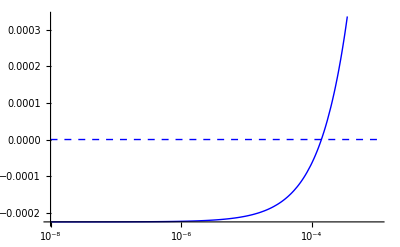

```mathematica
LogLinearPlot[{(a1 a2-a3)/.{γ->0.9,X->0.5,Y->0.4,ξH-> 0.1,ξP-> 1},0},{μ,10^-8,10^-3},PlotStyle->{Blue,{Blue,Dashed}}]
```

As long as the mutation rate is low there exists the potential for limit cycles. Below we use numerical integration to confirm that this unstable polymorphic equilibrium does indeed approach a limit cycles.

#### Host fixation equilibrium #1: {pH[t]→1,pP[t]→-(2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→-(2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)}

Finding the eigenvalues numerically under the same conditions that led to the potential for limit cycles above.

```mathematica
Eigenvalues[JMtrx[t]/.equilibria[[2]]/.Pars]//Simplify
```

{-0.990835,0.0908325,-0.0300006}

Under this parameter condition this equilibrium is unstable.

#### Host fixation equilibrium #2: {pH[t]→1,pP[t]→(-2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→(-2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)}

Finding the eigenvalues numerically under the same conditions that led to the potential for limit cycles above.

```mathematica
Eigenvalues[JMtrx[t]/.equilibria[[2]]/.Pars]//Simplify
```

{-0.990835,0.0908325,-0.0300006}

This equilibrium is unstable.

#### Host fixation equilibrium #3:{pH[t]→0,pP[t]→(2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→(2 μ+X ξP-Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)}

Finding the eigenvalues numerically under the same conditions that led to the potential for limit cycles above.

```mathematica
Eigenvalues[JMtrx[t]/.equilibria[[3]]/.Pars]//Simplify
```

{-0.785413,-0.114589,0.0299994}

Once again this equilibrium is unstable

#### Host fixation equilibrium #4: {pH[t]→0,pP[t]→-(-2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP),pM[t]→-(-2 μ-X ξP+Y ξP+√(4 μ^2+(X-Y)^2 ξP^2))/(2 (X-Y) ξP)}

Finding the eigenvalues numerically under the same conditions that led to the potential for limit cycles above.

```mathematica
Eigenvalues[JMtrx[t]/.equilibria[[4]]/.Pars]//Simplify
```

{-0.990835,0.0908325,-0.0300006}

This equilibrium is also unstable, hence confirming that limit cycles are likely under this condition.

### Numerical Integration

We numerically integrate this modified matching allele model for a given parameter combination given by Pars and initial allele frequencies given by Inits below.

```mathematica
Pars={X->0.45,Y->0.35,μ->1*10^-3,γ->0.246,ξH-> 0.36,ξP-> 1,tmax->5000};
```

Initial Conditions: For initial conditions we use the polymorphic equilibrium {1/2,1/2,1/2} with a small deviation.

```mathematica
Inits={pH[0]==0.5*0.9,pP[0]==0.5*1.2,pM[0]==0.5};
```

```mathematica
nsol=NDSolve[Join[ODE[t],Inits]/.Pars,Vars[t],{t,0,tmax/.Pars}]//Flatten;
pHsol[τ_]:=pH[t]/.nsol/.{t->τ}
pPsol[τ_]:=pP[t]/.nsol/.{t->τ}
pMsol[τ_]:=pM[t]/.nsol/.{t->τ}
```

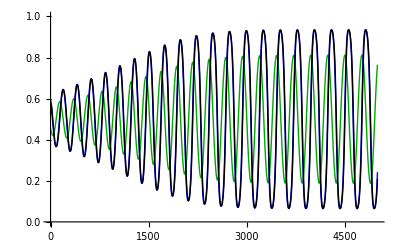

```mathematica
Plot[{pHsol[t],pPsol[τ],pMsol[τ]},{t,1,tmax/.Pars},PlotStyle->{{Darker[Green],Thick},Blue,{Black,Thick}},PlotRange->{0,1},AxesOrigin->{0,0}]
```

As expected given large γ the frequency of immature and mature parasites are approximately equal.  To relate γ to the epidemiological parameters in the models below we have:

```mathematica
γ[δ_,nI_,τI_]:=δ/(1-(nI/(nI+δ τI))^nI)
```

## SEIRS Model without Coevolution

```mathematica
Clear["Global`*"];
```

Here we derive an epidemiological which captures a maturation of pathogens by including an exposed class of individuals who are infected but not yet infectious themselves.  We find the equilibria of the model and assess their stability.

### The Differential Equations

We are interested in a epidemiological model where the host population is divided into susceptible individuals which become exposed upon infection but are not yet infectious.  Exposed individuals transition through nE stages before the host become infectious.  The host then experiences nI infectious stages until the host recovers.  Upon recovery resistance to infection lasts for a nR stages until the host looses immunity to disease and becomes susceptible once again.

Let the number of susceptible hosts at time t be s[t], the ODE for d/dt s[0,t]=f1[0,t]. In the absence of genetic variation within the host population, we have only one type of host, which we label “0”, as a placeholder.

```mathematica
f1[0,t_]:=b(s[0,t]+Sum[e[c,t],{c,1,nE}]+Sum[i[c,t],{c,1,nI}]+Sum[r[c,t],{c,1,nR}])(1-κ(s[0,t]+Sum[e[c,t],{c,1,nE}]+Sum[i[c,t],{c,1,nI}]+Sum[r[c,t],{c,1,nR}]))-d s[0,t]-β s[0,t]Sum[i[c,t],{c,1,nI}]+nR/τR r[nR,t]
```

Here b is the host birth rate, κ is the inverse of the carrying capacity, d is the host death rate.  Infectious individuals transmit infections to susceptible individuals at rate β whereas individuals from the last recovered stage, nR, return to the susceptible class at rate nR/τR.
Let the number of exposed individuals in stage c at time t be e[c,t], and the corresponding ODE for d/dt e[c,t]=f2[c,t].

```mathematica
f2[c_,t_]:=If[c==1,β s[0,t]Sum[i[j,t],{j,1,nI}]-(nE/τE+δ)e[c,t],nE/τE e[c-1,t]-(nE/τE+δ)e[c,t]]
```

New infections enter the first exposed stage whereas exposed stages 2 through nE depend only on the previous infected class, hence the ODEs for the first vs later classes have fundamentally different forms.  Hosts transition exit each exposed class at a rate nE/τE and die at a rate δ, where we assume δ>d.

Let the number of infected in class c at time t be i[c,t] ,  the ODE for d/dt i[c,t]=f3[c,t].  Once again since exposed individuals receive individuals from the last exposed class whereas the 2nd thorough nI infectious classes depend only on previous infectious classes and hence the ODEs for the first vs. later stages have distinct forms.

```mathematica
f3[c_,t_]:=If[c==1,nE/τE e[nE,t]-(nI/τI+δ)i[c,t],nI/τI i[c-1,t]-(nI/τI+δ)i[c,t]]
```

Here infectious individuals transition between stages at rate nI/τI.

Let the number of recovered in class c at time t be r[c,t], the ODE for d/dt r[c,t]=f4[c,t].  Once again the first and latter stages have distinctly different forms.

```mathematica
f4[c_,t_]:=If[c==1,nI/τI i[nI,t]-(nR/τR+d)r[c,t],nR/τR r[c-1,t]-(nR/τR+d)r[c,t]]
```

#### List of Equations

A list of the differential equations is given by:

```mathematica
ODEs[nEs_,nIs_,nRs_]:=Block[{nE,nI,nR,odes,j},odes={};nE=nEs;nI=nIs;nR=nRs;
AppendTo[odes,D[s[0,t],t]== f1[0,t]];
For[j=1,j≤nE,j++,
AppendTo[odes,D[e[j,t],t]== f2[j,t]];
];
For[j=1,j≤nI,j++,
AppendTo[odes,D[i[j,t],t]== f3[j,t]];
];
For[j=1,j≤nR,j++,
AppendTo[odes,D[r[j,t],t]== f4[j,t]];
];
odes
]
```

A list of the variables in the system is given by:

```mathematica
Vars[nEs_,nIs_,nRs_]:=Join[{s[0,t]},Table[e[c,t],{c,1,nEs}],Table[i[c,t],{c,1,nIs}],Table[r[c,t],{c,1,nRs}]]
```

### Equilibria

#### Deriving the equilibrium equations

Let se be the abundance of susceptible individuals at equilibrium, ee[c] the abundance of exposed individuals in stage c at equilibrium, ie[c] and re[c] the abundances of infected and recovered individuals at equilibrium.  At equilibrium the recovered equations, the infected equations and the 2nd through nEth infected stages can be written in terms of the first exposed class. Letting the abundance of individuals in the first exposed class be ee1 we can write:

```mathematica
re[c_]:=(nR/(nR+d τR))^(c-1)(nI/τI(τR/(nR+d τR)))(nI/(nI+δ τI))^(nI-1)(nE/τE(τI/(nI+δ τI)))(nE/(nE+δ τE))^(nE-1)ee[1]
```

for c={1,2...nR},

```mathematica
ie[c_]:=(nI/(nI+δ τI))^(c-1)(nE/τE(τI/(nI+δ τI)))(nE/(nE+δ τE))^(nE-1)ee[1]
```

for c={1,2...nI} and,

```mathematica
ee[c_]:=If[c>1,(nE/(nE+δ τE))^(c-1)ee[1],ee1]
```

for c={1,2...nE}.

Hence we can reduce the equilibrium down to 2 equations, the susceptible equation and the first infected equation by expressing the sums over infected classes in terms of the first infected class only.  To do this we define zE,zI,zR and znR such that:
∑_(j=1)^nE ee[j]=zE ee1
∑_(j=1)^nI ie[j]=zI ee1
∑_(j=1)^nR re[j]=zR ee1 and
re[nR]=znR ee1

```mathematica
zsub={zE->Sum[ee[j],{j,1,nE}]/ee1,zI->Sum[ie[j],{j,1,nI}]/ee1,zR->Sum[re[j],{j,1,nR}]/ee1,znR->re[nR]/ee1}//Simplify
```

{zE→(nE+δ τE-nE^nE (nE+δ τE)^(1-nE))/(δ τE),zI→-(nE (nE/(nE+δ τE))^(-1+nE) (-1+(nI/(nI+δ τI))^nI))/(δ τE),zR→-(nE (nE/(nE+δ τE))^(-1+nE) (nI/(nI+δ τI))^nI (-1+(nR/(nR+d τR))^nR))/(d τE),znR→(nE (nE/(nE+δ τE))^(-1+nE) (nI/(nI+δ τI))^nI τR (nR/(nR+d τR))^nR)/(nR τE)}

The remaining two equations which are equal to 0 at equilibrium are:

```mathematica
F1=b(se+(zE+zI+zR)ee1)(1-κ(se+(zE+zI+zR)ee1))-d se-β se zI ee1+nR/τR znR ee1;
F2=β se zI ee1-(nE/τE+δ)ee1;
```

```mathematica
EquiSol=Solve[{F1==0,F2==0},{se,ee1}]//Simplify
```

{{se→0,ee1→0},{se→(b-d)/(b κ),ee1→0},{se→(nE+δ τE)/(zI β τE),ee1→-((-nR zI^2 znR β^2 τE^2+nE zI^2 β^2 τE τR+2 b nE zE zI β κ τE τR+2 b nE zI^2 β κ τE τR+2 b nE zI zR β κ τE τR-b zE zI^2 β^2 τE^2 τR-b zI^3 β^2 τE^2 τR-b zI^2 zR β^2 τE^2 τR+zI^2 β^2 δ τE^2 τR+2 b zE zI β δ κ τE^2 τR+2 b zI^2 β δ κ τE^2 τR+2 b zI zR β δ κ τE^2 τR+√(zI^2 β^2 τE^2 (-4 b (zE+zI+zR)^2 κ (nE+δ τE) (d zI β τE+b (nE κ-zI β τE+δ κ τE)) τR^2+(nR zI znR β τE-(nE (2 b (zE+zR) κ+zI (β+2 b κ))+(zI β δ-b (zE+zI+zR) (zI β-2 δ κ)) τE) τR)^2)))/(2 b zI^2 (zE+zI+zR)^2 β^2 κ τE^2 τR))},{se→(nE+δ τE)/(zI β τE),ee1→(nR zI^2 znR β^2 τE^2-nE zI^2 β^2 τE τR-2 b nE zE zI β κ τE τR-2 b nE zI^2 β κ τE τR-2 b nE zI zR β κ τE τR+b zE zI^2 β^2 τE^2 τR+b zI^3 β^2 τE^2 τR+b zI^2 zR β^2 τE^2 τR-zI^2 β^2 δ τE^2 τR-2 b zE zI β δ κ τE^2 τR-2 b zI^2 β δ κ τE^2 τR-2 b zI zR β δ κ τE^2 τR+√(zI^2 β^2 τE^2 (-4 b (zE+zI+zR)^2 κ (nE+δ τE) (d zI β τE+b (nE κ-zI β τE+δ κ τE)) τR^2+(nR zI znR β τE-(nE (2 b (zE+zR) κ+zI (β+2 b κ))+(zI β δ-b (zE+zI+zR) (zI β-2 δ κ)) τE) τR)^2)))/(2 b zI^2 (zE+zI+zR)^2 β^2 κ τE^2 τR)}}

#### Biological validity of endemic equilibria

As with the SIRS model here we derive the conditions for which only a single endemic equilibrium is biologically valid, ie positive.  When this condition is not met we show numerically that both endemic equilibria are either negative of complex and hence neither is biologically valid.

Condition for which only one endemic equilibrium is biologically valid.

As with the SIRS model at the endemic equilibrium ee1 must satisfy the following quadratic.  By dividing through by the coefficient of ee1^2 we ensure that the quadratic is upward facing.

```mathematica
Quad[ee1s_]:=Collect[(F1/.se->(nE+δ τE)/(zI β τE))/(CoefficientList[F1/.se->(nE+δ τE)/(zI β τE),ee1][[3]]),ee1,Simplify]/.ee1->ee1s
```

```mathematica
Quad[ee1]
```

ee1^2+((nE+δ τE) (d zI β τE+b (nE κ-zI β τE+δ κ τE)))/(b zI^2 (zE+zI+zR)^2 β^2 κ τE^2)-(ee1 (b (zE+zI+zR)-(nE+δ τE)/τE-(2 b (zE+zI+zR) κ (nE+δ τE))/(zI β τE)+(nR znR)/τR))/(b (zE+zI+zR)^2 κ)

If the Y-intercept of this quadratic is negative we are guaranteed that one endemic equilibrium will be negative (biologically invalid) and one will be positive (biologically valid).  In particular we solve for the critical value of β for which the Y-intercept is 0.

```mathematica
Simplify[Flatten[Solve[(Quad[0]/.zsub)==0,β]]]
```

{β→-(b δ κ (nE/(nE+δ τE))^-nE)/((b-d) (-1+(nI/(nI+δ τI))^nI))}

When β is larger than this critical value we will have only one biologically valid equilibrium.  When β is less than this critical value and hence the Y-intercept is positive than either both equilibria are positive, both are negative, or both are complex.  Below we show numerically that for a large number of parameter combinations that the slope of the quadratic at ee1=0 is positive.  This ensures that both equilibria are either negative or complex and hence neither is biologically valid.

Numerical demonstration that both equilibria are not biologically valid

```mathematica
Slope=D[Quad[ee1],ee1]/.ee1->0/.zsub//Simplify;
```

```mathematica
Module[{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,βs,c,parsSub},NegList={};PosList={};
For[c=1,c≤5000,c++,
(*Drawing values*)
nEs=Random[Integer,{1,50}];nIs=Random[Integer,{1,50}];nRs=Random[Integer,{1,50}];
τEs=Random[Real,{1,40}];τIs=Random[Real,{1,40}];τRs=Random[Real,{20,100}];
bs=Random[Real,{0.01,0.2}];ds=Random[Real,{0.001,bs}];δs=Random[Real,{ds,ds+0.1}];
parsSub={nE->nEs,nI->nIs,nR->nRs,τE->τEs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,β->1,κ->1};
βs=Random[Real,{0.01,-(b δ κ (nE/(nE+δ τE))^-nE)/((b-d) (-1+(nI/(nI+δ τI))^nI))/.parsSub}];
parsSub={nE->nEs,nI->nIs,nR->nRs,τE->τEs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,β->βs,κ->1};test=(Slope/.parsSub);
If[test<0,AppendTo[NegList,{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,βs,test}],AppendTo[PosList,{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,βs,test}]]
]
]
```

```mathematica
NegList
```

{}

```mathematica
Length[PosList]
```

5000

For the 5000 randomly chosen parameter conditions for which the intercept is positive (β<-(b δ κ (nE/(nE+δ τE))^-nE)/((b-d) (-1+(nI/(nI+δ τI))^nI))) the slope at ee1=0 is positive and hence both equilibria are either negative or complex.

#### List of equilibria

Above we solved for the equilibrium values of the susceptible class, se, and the first infected class, ee1.  Given these expressions below we construct a substitution list for all classes for equilibrium number num. The first equilibrium is host extinction, the second is disease extinction, the third and fourth are the endemic equilibria.

```mathematica
EquiSub[nEs_,nIs_,nRs_,num_]:=Block[{equList,c},equList={};
AppendTo[equList,s[0,∞]->se];
AppendTo[equList,e[1,∞]->ee1];
For[c=2,c≤nEs,c++,
AppendTo[equList,e[c,∞]->ee[c]];
];
For[c=1,c≤nIs,c++,
AppendTo[ equList,i[c,∞]->ie[c]];
];
For[c=1,c≤nRs,c++,
AppendTo[equList,r[c,∞]->re[c]];
];
equList/.EquiSol[[num]]/.zsub/.{nE->nEs,nI->nIs,nR->nRs}
]
```

#### Relationship between the parameters

As with the SIRS model, in order to develop analogous coevolutionary and epidemiological models we must define some logical relationship between the parameters. In particular we let ξP=1, the fitness of successful pathogen, similarly ξH is the fitness cost of infection which in the SEIRS model is given by ξH=δ(nE+nI).  Finally, the maturation rate could be defined as either a) the flow into the first infected stage relative to the total number of infections or b) the total flow out of the infectious class relative to the total number of infections.  Because choice a leads to a simpler relationship this is what we use.  Specifically, at equilibrium  the flow into the first infectious class is nE/τE ee[nE] whereas the total abundance of the infectious class is ee[nE]∑_(c=1)^nI (nI/(nI+δ τI))^(c-1)(nE/τE(τI/(nI+δ τI)))

```mathematica
(nE/τE ee[nE])/(ee[nE]∑_(c=1)^nI (nI/(nI+δ τI))^(c-1)(nE/τE(τI/(nI+δ τI))))//Simplify
```

-δ/(-1+(nI/(nI+δ τI))^nI)

```mathematica
γ[nI_,δ_,τI_]:=-δ/(-1+(nI/(nI+δ τI))^nI)
```

Given our assumption that γ is large this is most likely to be satisfied where τI and nI are small and δ large.

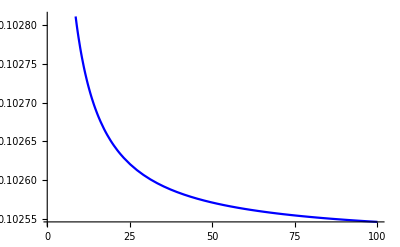

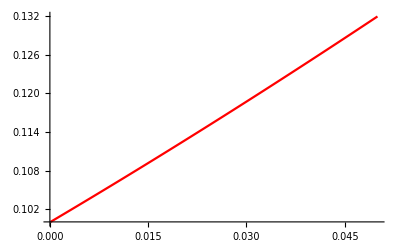

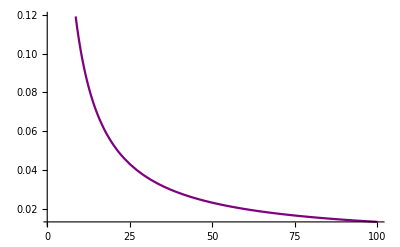

```mathematica
nIPlot=Plot[{γ[nI,δ,τI]/.{δ->0.005,τI->10}},{nI,1,100},PlotStyle->Blue]
δPlot=Plot[{γ[nI,δ,τI]/.{nI->5,τI->10}},{δ,0.0001,0.05},PlotStyle->Red]
τIPlot=Plot[{γ[nI,δ,τI]/.{δ->0.005,nI->5}},{τI,1,100},PlotStyle->Purple]
```

### Stability

To evaluate the stability of the equilibria found above we first construct a Jacobian matrix.

```mathematica
Jmtrx[nEs_,nIs_,nRs_]:=Block[{ii,jj,nE,nI,nR,jmtrx},
nE=nEs;nI=nIs;nR=nRs;jmtrx=Table[{},{ii,1,1+nE+nI+nR}];
(*Suscetible equation*)
AppendTo[jmtrx[[1]],D[f1[0,t],s[0,t]]];
For[ii=1,ii≤nE,ii++,AppendTo[jmtrx[[1]],D[f1[0,t],e[ii,t]]]];
For[ii=1,ii≤nI,ii++,AppendTo[jmtrx[[1]],D[f1[0,t],i[ii,t]]]];
For[ii=1,ii≤nR,ii++,AppendTo[jmtrx[[1]],D[f1[0,t],r[ii,t]]]];
(*exposed equation*)
For[jj=1,jj≤ nE,jj++,
AppendTo[jmtrx[[1+jj]],D[f2[t,jj],s[t,0]]];
For[ii=1,ii≤nE,ii++,AppendTo[jmtrx[[1+jj]],D[f2[jj,t],e[ii,t]]]];
For[ii=1,ii≤nI,ii++,AppendTo[jmtrx[[1+jj]],D[f2[jj,t],i[ii,t]]]];
For[ii=1,ii≤nR,ii++,AppendTo[jmtrx[[1+jj]],D[f2[jj,t],r[ii,t]]]];
];
(*infected equation*)
For[jj=1,jj≤ nI,jj++,
AppendTo[jmtrx[[1+nE+jj]],D[f3[t,jj],s[t,0]]];
For[ii=1,ii≤nE,ii++,AppendTo[jmtrx[[1+nE+jj]],D[f3[jj,t],e[ii,t]]]];
For[ii=1,ii≤nI,ii++,AppendTo[jmtrx[[1+nE+jj]],D[f3[jj,t],i[ii,t]]]];
For[ii=1,ii≤nR,ii++,AppendTo[jmtrx[[1+nE+jj]],D[f3[jj,t],r[ii,t]]]];
];
(*recovered equation*)
For[jj=1,jj≤ nR,jj++,
AppendTo[jmtrx[[1+nE+nI+jj]],D[f4[t,jj],s[t,0]]];
For[ii=1,ii≤nE,ii++,AppendTo[jmtrx[[1+nE+nI+jj]],D[f4[jj,t],e[ii,t]]]];
For[ii=1,ii≤nI,ii++,AppendTo[jmtrx[[1+nE+nI+jj]],D[f4[jj,t],i[ii,t]]]];
For[ii=1,ii≤nR,ii++,AppendTo[jmtrx[[1+nE+nI+jj]],D[f4[jj,t],r[ii,t]]]];
];
jmtrx=jmtrx/.{t->∞}
]
```

Like with the SIRS model, we are not able to solve for the eigenvalues in general but we can do numerically as well as analytically in a few simple cases.

#### Extinction

The characteristic polynomial at this equilibrium is straightforward:

```mathematica
CharPoly[nE_,nI_,nR_]:=((b-d)-λ)(-(δ+2/τE)-λ)^nE(-(δ+2/τI)-λ)^nI(-(d+2/τR)-λ)^nR
```

Hence the roots will be λ=b-d, λ=-(δ+2/τE),λ=-(δ+2/τI), and λ=-(d+2/τR).  Since b-d is positive as long as b>d (which we will assume is true) this equilibrium is unstable.

#### Disease Extinction:

As with the SIRS model we can proceed analytically here as well.  The characteristic polynomial can be written as: (AA - λ) (KK - λ)^nR Det[M[nE,nI] ] where M[nE,nI] is given by the following

```mathematica
M[nEs_,nIs_]:=Block[{nE,nI,mtrx,j,k},nE=nEs;nI=nIs;mtrx=Table[0,{j,1,nE+nI},{k,1,nE+nI}];
For[j=1,j≤nE,j++,mtrx[[j,j]]=FF-λ;mtrx[[j+1,j]]=HH];
For[j=nE+1,j≤nE+nI,j++,mtrx[[j,j]]=II-λ;mtrx[[1,j]]=GG];
For[j=nE+1,j<nE+nI,j++,mtrx[[j+1,j]]=JJ];
mtrx
]
```

In order for the this matrix to have an eigenvalue of 0 the constant term of its characteristic polynomial must be 0.  This constant term can be written as a function of nE and nI in the following way:

```mathematica
S[nE_,nI_]:=FF^nE II^nI+GG(-HH)^nE Sum[II^i(-JJ)^(nI-1-i),{i,0,nI-1}]
```

Where the letters are given by:

```mathematica
letters={FF->-(δ+nE/τE),HH-> nE/τE,II -> -(δ+nI/τI),JJ->nI/τI,GG-> ((b-d) β)/(b κ)};
```

For any nE and nI this constant term simplifies to 0.

```mathematica
FullSimplify[Numerator[Factor[S[nE,nI]/.letters/.β->-(b δ κ (nE/(nE+δ τE))^-nE)/((b-d) (-1+(nI/(nI+δ τI))^nI))]],{Element[nI,Integers],Element[nE,Integers]}]
```

0

#### Endemic equilibrium

We can numerically evaluate the stability of the biologically valid endemic equilibrium (equilibrium #4) as shown for the specific parameter condition give by Pars.

```mathematica
Pars={nE->2,nI->10,nR->5,τE->10,τI->10,τR->23,β->0.5,d->0.001,δ->0.001,κ->1,b->0.02};
```

```mathematica
Sort[Eigenvalues[Jmtrx[2,10,5]/.EquiSub[2,10,20,4]/.Pars]]//Chop
```

{-1.52371,-1.44714-0.282531 ⅈ,-1.44714+0.282531 ⅈ,-1.2339-0.493287 ⅈ,-1.2339+0.493287 ⅈ,-0.928576-0.575737 ⅈ,-0.928576+0.575737 ⅈ,-0.587766-0.500708 ⅈ,-0.587766+0.500708 ⅈ,-0.246772-0.300699 ⅈ,-0.246772+0.300699 ⅈ,-0.218391,-0.218391,-0.218391,-0.218391,-0.218391,-0.0946153,0}

At this point the endemic equilibrium is stable with damped cycles.

### Numerical Integration

Here we numerically integrate the system of ODEs for the particular parameter conditions given by Pars

```mathematica
Pars={nE->2,nI->10,nR->5,τE->10,τI->10,τR->23,β->0.5,d->0.001,δ->0.001,κ->1,b->0.02,tmax->300};
```

For initial conditions we start the system close to the biologically valid endemic (equilibrium 4).

```mathematica
Inits[nEs_,nIs_,nRs_]:=Block[{nE,nI,nR,inits,j},inits={};nE=nEs;nI=nIs;nR=nRs;
AppendTo[inits,s[0,0]== 0.9*s[0,∞]];
For[j=1,j≤nE,j++,
AppendTo[inits,e[j,0]== 1.2*e[j,∞]];
];
For[j=1,j≤nI,j++,
AppendTo[inits,i[j,0]==  1.2*i[j,∞]];
];
For[j=1,j≤nR,j++,
AppendTo[inits,r[j,0]==r[j,∞]];
];
inits/.EquiSub[nE,nI,nR,4]/.Pars
]
```

```mathematica
nsol=NDSolve[Join[ODEs[ nE/.Pars,nI/.Pars,nR/.Pars]/.Pars,Inits[ nE/.Pars,nI/.Pars,nR/.Pars]],Vars[nE/.Pars,nI/.Pars,nR/.Pars],{t,0,tmax/.Pars}]//Flatten;
```

```mathematica
ssol[0,τ_]:=s[0,t]/.nsol/.t->τ
esol[c_,τ_]:=e[c,t]/.nsol/.t->τ
isol[c_,τ_]:=i[c,t]/.nsol/.t->τ
rsol[c_,τ_]:=r[c,t]/.nsol/.t->τ
```

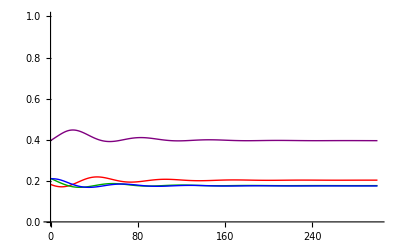

```mathematica
Plot[{ssol[0,t],Sum[esol[c,τ],{c,1,nE/.Pars}],Sum[isol[c,τ],{c,1,nI/.Pars}],Sum[rsol[c,τ],{c,1,nR/.Pars}]},{t,0,tmax/.Pars},PlotRange->{0,1},PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick},{Purple,Thick}}]
```

Here susceptible hosts are shown in red, exposed in green, infected in blue and recovered in purple.

## SERIS with Coevolution

```mathematica
Clear["Global`*"];
```

Using the same epidemiological framework as above we now incorporate host-parasite coevolution by introducing two hosts and two pathogen types as in the matching alleles model.  We find the equilibria of the resulting system and asses their stability.

### The Differential Equations

We are interested in two host types, 1 and 2, that are born susceptible.  As above, upon infection hosts become exposed but not yet infectious, they progress through a series of exposed stages before becoming infectious.  They then experience a number of infectious stage before recovery and finally after progressing through a number of recovered stages return once again to the susceptible class.  Denoting the two susceptible host types by s[h,t] where h={1,2} let d/dt s[h,t]=f1[h,t].

```mathematica
f1[h_,t_]:=b*(s[h,t]+Sum[e[h,l,j,t],{l,1,2},{j,1,nE}]+Sum[i[h,l,j,t],{l,1,2},{j,1,nI}]+Sum[r[h,j,t],{j,1,nR}])*(1-κ*(Sum[s[k,t],{k,1,2}]+Sum[e[k,l,j,t],{k,1,2},{l,1,2},{j,1,nE}]+Sum[i[k,l,j,t],{k,1,2},{l,1,2},{j,1,nI}]+Sum[r[k,j,t],{k,1,2},{j,1,nR}]))-d*s[h,t]+nR/τR r[h,nR,t]-s[h,t]Sum[β[h,l]Sum[i[k,l,j,t],{k,1,2},{j,1,nI}],{l,1,2}]
```

Most parameters are as defined above. Here β[h,p] denotes the transmission rate of pathogen type p to host type h and μ is the rate at which pathogens mutate from type 1 to type 2.  Here e[h,p,c,t] denotes the density of hosts of type h exposed to pathogens of type p in stage exposed stage c at time t.  Similarly i[h,p,c,t] is the density of type h infectious hosts who carry pathogen p in infectious stage c at time t. Finally, r[h,c,t] is the density of recovered hosts of type h in stage c at time t.

Let the differential equation for exposed stages be given by d/dt e[h,p,c,t]=f2[h,p,c,t]

```mathematica
f2[h_,p_,c_,t_]:=If[c==1,s[h,t]((1-μ)β[h,p]Sum[i[k,p,j,t],{k,1,2},{j,1,nI}]+μ β[h,3-p] Sum[i[k,3-p,j,t],{k,1,2},{j,1,nI}])-(δ+nE/τE) e[h,p,c,t],nE/τE e[h,p,c-1,t]-(δ+nE/τE) e[h,p,c,t]];
```

As above the ODE for the first exposed stage has a distinctly different form from the latter stages, this holds true for d/dt i[h,p,c,t] and d/dt r[h,c,t] as well.

Let d/dt i[h,p,c,t]=f3[h,p,c,t] and d/dt r[h,c,t]=f4[h,c,t]

```mathematica
f3[h_,p_,c_,t_]:=If[c==1,nE/τE e[h,p,nE,t]-(δ+nI/τI) i[h,p,c,t],nI/τI i[h,p,c-1,t]-(δ+nI/τI) i[h,p,c,t]]
```

```mathematica
f4[h_,c_,t_]:=If[c==1,nI/τI Sum[i[h,l,nI,t],{l,1,2}]-(d+nR/τR)r[h,c,t],nR/τR r[h,c-1,t]-(d+nR/τR)r[h,c,t]]
```

For simplicity we will assume a symmetric matching alleles model such that  β[1,1]=β[2,2]=X and  β[1,2]=β[2,1]=Y.

```mathematica
βsub={β[1,1]->X,β[2,2]->X,β[1,2]->Y,β[2,1]->Y};
```

#### List of Differential Equations

A complete list of the differential equations above is given by:

```mathematica
ODEs[nEs_,nIs_,nRs_]:=Block[{nE,nI,nR,odes,h,p,c},odes={};nE=nEs;nI=nIs;nR=nRs;
For[h=1,h≤2,h++,
AppendTo[odes,D[s[h,t],t]== f1[h,t]]
];
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nE,c++,
AppendTo[odes,D[e[h,p,c,t],t]== f2[h,p,c,t]]
];
];
];
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nI,c++,
AppendTo[odes,D[i[h,p,c,t],t]== f3[h,p,c,t]]
];
];
];
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,
AppendTo[odes,D[r[h,c,t],t]== f4[h,c,t]]
];
];
odes=odes/.βsub
]
```

A list of the variables is given by:

```mathematica
Vars[nEs_,nIs_,nRs_]:=Block[{nE,nI,nR,vars,h,p,c},vars={};nE=nEs;nI=nIs;nR=nRs;
For[h=1,h≤2,h++,AppendTo[vars,s[h,t]]];
For[h=1,h≤2,h++,For[p=1,p≤2,p++,For[c=1,c≤nE,c++,AppendTo[vars,e[h,p,c,t]]]]];
For[h=1,h≤2,h++,For[p=1,p≤2,p++,For[c=1,c≤nI,c++,AppendTo[vars,i[h,p,c,t]]]]];
For[h=1,h≤2,h++,For[c=1,c≤nR,c++,AppendTo[vars,r[h,c,t]]]];
vars
]
```

### Equilibria

As with the SEIRS model without coevolution at equilibrium we can express the each exposed, infected, and recovered class in terms of the first exposed class only.  This will allow us to reduce the system of equations down to 6, 2 susceptible equations (2 host types) and the first 4 exposed equations (2 host and 2 pathogen types).  The density of exposed (ee[h,p,c]), infected (ie[h,p,c]) and recovered (re[h,c]) stages at equilibrium as a function of the first exposed stage ee1[h,p] are given by:

```mathematica
re[h_,c_]:=(nR/(nR+d τR))^(c-1)(nI/τI(τR/(nR+d τR)))(nI/(nI+δ τI))^(nI-1)(nE/τE(τI/(nI+δ τI)))(nE/(nE+δ τE))^(nE-1)(ee1[h,1]+ee1[h,2])
```

for c={1,2...nR},

```mathematica
ie[h_,p_,c_]:=(nI/(nI+δ τI))^(c-1)(nE/τE(τI/(nI+δ τI)))(nE/(nE+δ τE))^(nE-1)ee1[h,p]
```

for c={1,2...nI} and,

```mathematica
ee[h_,p_,c_]:=If[c>1,(nE/(nE+δ τE))^(c-1)ee1[h,p],ee1[h,p]]
```

for c={1,2...nE}.

We can express the 2 susceptible differential equations and the first stage exposed odes in terms of the susceptible class and first exposed stage only by defining
(∑_(j=1))^nE e[h,p,j,t]=zE e[h,p,1,t]
(∑_(j=1))^nE i[h,p,j,t]=zI e[h,p,1,t]
(∑_(j=1))^nE r[h,j,t]=zR( e[h,1,1,t]+ e[h,2,1,t])
r[h,nR,t]=znR( e[h,1,1,t]+ e[h,2,1,t])
and solving for zE, zI, zR and znR.

```mathematica
zsub={zE-> Sum[ee[h,p,j],{j,1,nE}]/ee1[h,p],zI-> Sum[ie[h,p,j],{j,1,nI}]/ee1[h,p],zR-> Sum[re[h,j],{j,1,nR}]/(ee1[h,1]+ee1[h,2]),znR-> re[h,nR]/(ee1[h,1]+ee1[h,2])}//Simplify
```

{zE→(nE+δ τE-nE^nE (nE+δ τE)^(1-nE))/(δ τE),zI→-(nE (nE/(nE+δ τE))^(-1+nE) (-1+(nI/(nI+δ τI))^nI))/(δ τE),zR→-(nE (nE/(nE+δ τE))^(-1+nE) (nI/(nI+δ τI))^nI (-1+(nR/(nR+d τR))^nR))/(d τE),znR→(nE (nE/(nE+δ τE))^(-1+nE) (nI/(nI+δ τI))^nI τR (nR/(nR+d τR))^nR)/(nR τE)}

The remaining equilibrium equations are given by:

```mathematica
f1e[h_]:=b*(se[h]+(zE+zI+zR)(ee1[h,1]+ee1[h,2]))*(1-κ Sum[(se[k]+(zE+zI+zR)(ee1[k,1]+ee1[k,2])),{k,1,2}])-d se[h]+nR/τR znR (ee1[h,1]+ee1[h,2])-se[h]Sum[β[h,l]zI ee1[k,l],{k,1,2},{l,1,2}]
f2e[h_,p_]:=se[h]((1-μ)β[h,p]Sum[zI ee1[k,p],{k,1,2}]+μ β[h,3-p]Sum[zI ee1[k,3-p],{k,1,2}])-(δ+nE/τE)ee1[h,p]
```

To solve for the equilibria is it convenient to find a list of expressions that must equal zero at equilibrium.

```mathematica
EquiList=Flatten[Join[Table[f1e[k],{k,1,2}],Table[f2e[k,l],{k,1,2},{l,1,2}]]]/.βsub;
```

The variables we are solving for are given by the list

```mathematica
EquiVars=Flatten[Join[Table[se[k],{k,1,2}],Table[ee1[k,l],{k,1,2},{l,1,2}]]]
```

{se[1],se[2],ee1[1,1],ee1[1,2],ee1[2,1],ee1[2,2]}

Solving for these equilibria is unfortunately not as straightforward as using Solve however.  Instead we must break down the equilibria into the various possibilities. Specifically if we consider the four exposed types (ee1[1,1], ee1[1,2], ee1[2,1], ee1[2,2]) then at the equilibrium there may be either 0 infections types present, or 1,2,3, or 4 types present.

#### Option 1: No infections present (∞ number of solutions)

Because there are no infections present we have the following

```mathematica
Sub1=Flatten[Table[ee1[k,l]->0,{k,1,2},{l,1,2}]]
```

{ee1[1,1]→0,ee1[1,2]→0,ee1[2,1]→0,ee1[2,2]→0}

Simplifying the list of equilibrium expressions

```mathematica
EquList1=(EquiList/.zsub)/.Sub1//Simplify
```

{-se[1] (d+b (-1+κ (se[1]+se[2]))),-se[2] (d+b (-1+κ (se[1]+se[2]))),0,0,0,0}

Solving expression 1 for se[2]

```mathematica
SolA=Solve[EquList1[[1]]==0,se[2]]//Simplify//Flatten
```

{se[2]→(b-d-b κ se[1])/(b κ)}

Substituting back into the list of expressions we see that this satisfies all the equations

```mathematica
EquList1/.SolA//Simplify
```

{0,0,0,0,0,0}

Hence any solution that satisfies {se[2]→(b-d-b κ se[1])/(b κ)} satisfies all the equations, this leads to an infinite number of possible solutions.

```mathematica
Equilbrium1=EquiVars/.Sub1/.SolA
```

{se[1],(b-d-b κ se[1])/(b κ),0,0,0,0}

#### Option 2: Single infection type present (No solutions)

Although there are technically four possible single type infections that could be present at equilibria by taking advantage of the symmetry of the problem and relabeling type 1 and type 2 pathogens we have only two possibilities, ee1[1,1]≠0 and ee1[1,2]≠0.

Option 2a: ee1[1,1]≠0

We can simplify the equilibrium expressions given the assumptions of this option.

```mathematica
Sub2a={ee1[1,2]->0,ee1[2,1]->0,ee1[2,2]->0};
```

```mathematica
EquiList2a=EquiList/.Sub2a//Simplify
```

{(nR znR ee1[1,1])/τR-d se[1]-X zI ee1[1,1] se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+se[1]+se[2])),se[2] (-d-Y zI ee1[1,1]+b (1-κ ((zE+zI+zR) ee1[1,1]+se[1]+se[2]))),-(ee1[1,1] (nE+τE (δ+X zI (-1+μ) se[1])))/τE,X zI μ ee1[1,1] se[1],-Y zI (-1+μ) ee1[1,1] se[2],Y zI μ ee1[1,1] se[2]}

Solving expression 6 for se[2] (note we know ee1[1,1] can not satisfy this equation as it is not 0) and substituting back into the list of expressions

```mathematica
subse2=Solve[EquiList2a[[6]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
EquiList2a/.subse2//Simplify
```

{(nR znR ee1[1,1])/τR-d se[1]-X zI ee1[1,1] se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+se[1])),0,-(ee1[1,1] (nE+τE (δ+X zI (-1+μ) se[1])))/τE,X zI μ ee1[1,1] se[1],0,0}

Solving expression 4 for se[1].

```mathematica
subse1=Solve[(EquiList2a/.subse2)[[4]]==0,se[1]]//Flatten
```

{se[1]→0}

```mathematica
EquiList2a/.subse2/.subse1//Simplify
```

{ee1[1,1] ((nR znR)/τR+b (zE+zI+zR) (1-(zE+zI+zR) κ ee1[1,1])),0,-((nE+δ τE) ee1[1,1])/τE,0,0,0}

Expression 3 is satisfied only when ee1[1,1]=0 which is not allowed hence there are no possible equilibria of this type.

Option 2b: ee1[1,2]≠0

We can simplify the equilibrium expressions given the assumptions of this option.

```mathematica
Sub2b={ee1[1,1]->0,ee1[2,1]->0,ee1[2,2]->0};
```

```mathematica
EquiList2b=EquiList/.Sub2b//Simplify
```

{(nR znR ee1[1,2])/τR-d se[1]-Y zI ee1[1,2] se[1]+b ((zE+zI+zR) ee1[1,2]+se[1]) (1-κ ((zE+zI+zR) ee1[1,2]+se[1]+se[2])),se[2] (-d-X zI ee1[1,2]+b (1-κ ((zE+zI+zR) ee1[1,2]+se[1]+se[2]))),Y zI μ ee1[1,2] se[1],-(ee1[1,2] (nE+τE (δ+Y zI (-1+μ) se[1])))/τE,X zI μ ee1[1,2] se[2],-X zI (-1+μ) ee1[1,2] se[2]}

Solving expression 6 for se[2] and substituting back into the list of expressions

```mathematica
subse2=Solve[EquiList2b[[6]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
EquiList2b/.subse2//Simplify
```

{(nR znR ee1[1,2])/τR-d se[1]-Y zI ee1[1,2] se[1]+b ((zE+zI+zR) ee1[1,2]+se[1]) (1-κ ((zE+zI+zR) ee1[1,2]+se[1])),0,Y zI μ ee1[1,2] se[1],-(ee1[1,2] (nE+τE (δ+Y zI (-1+μ) se[1])))/τE,0,0}

Solving expression 3 for se[1].

```mathematica
subse1=Solve[(EquiList2b/.subse2)[[3]]==0,se[1]]//Flatten
```

{se[1]→0}

```mathematica
EquiList2b/.subse2/.subse1//Simplify
```

{ee1[1,2] ((nR znR)/τR+b (zE+zI+zR) (1-(zE+zI+zR) κ ee1[1,2])),0,0,-((nE+δ τE) ee1[1,2])/τE,0,0}

Expression 4 can only be satisfied when ee1[1,2]=0 which is not allowed, hence there are no equilibria of this type.

#### Option 3: Two infection types present (No solutions)

By relabeling 1s and 2s there are 4 possible ways to choose 2 solutions a) {ee1[1,1]≠0, ee1[1,2]≠0} b) {ee1[1,1]≠0, ee1[2,1]≠0} c) {ee1[1,1]≠0, ee1[2,2]≠0} or d) {ee1[1,2]≠0, ee1[2,1]≠0}

Option 3a: {ee1[1,1]≠0, ee1[1,2]≠0}

```mathematica
Sub3a={ee1[2,1]->0,ee1[2,2]->0};
```

```mathematica
EquiList3a=EquiList/.Sub3a
```

{(nR znR (ee1[1,1]+ee1[1,2]))/τR-d se[1]-(X zI ee1[1,1]+Y zI ee1[1,2]) se[1]+b ((zE+zI+zR) (ee1[1,1]+ee1[1,2])+se[1]) (1-κ ((zE+zI+zR) (ee1[1,1]+ee1[1,2])+se[1]+se[2])),-d se[2]-(Y zI ee1[1,1]+X zI ee1[1,2]) se[2]+b se[2] (1-κ ((zE+zI+zR) (ee1[1,1]+ee1[1,2])+se[1]+se[2])),-(δ+nE/τE) ee1[1,1]+(X zI (1-μ) ee1[1,1]+Y zI μ ee1[1,2]) se[1],-(δ+nE/τE) ee1[1,2]+(X zI μ ee1[1,1]+Y zI (1-μ) ee1[1,2]) se[1],(Y zI (1-μ) ee1[1,1]+X zI μ ee1[1,2]) se[2],(Y zI μ ee1[1,1]+X zI (1-μ) ee1[1,2]) se[2]}

Solving equation 6 for ee1[1,2]

```mathematica
sub12=Solve[EquiList3a[[6]]==0,ee1[1,2]]//Flatten
```

{ee1[1,2]→(Y μ ee1[1,1])/(X (-1+μ))}

```mathematica
EquiList/.Sub3a/.sub12//Simplify
```

{(nR znR (1+(Y μ)/(X (-1+μ))) ee1[1,1])/τR-d se[1]-(zI (X^2+(Y^2 μ)/(-1+μ)) ee1[1,1] se[1])/X+b ((zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]+se[1]+se[2])),se[2] (-d-Y zI ee1[1,1]-(Y zI μ ee1[1,1])/(-1+μ)+b (1-κ ((zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]+se[1]+se[2]))),ee1[1,1] (-δ-nE/τE+(zI (X^2-X^2 μ+(Y^2 μ^2)/(-1+μ)) se[1])/X),-(μ ee1[1,1] (nE Y+τE (Y δ-X^2 zI (-1+μ) se[1]+Y^2 zI (-1+μ) se[1])))/(X (-1+μ) τE),(Y zI (-1+2 μ) ee1[1,1] se[2])/(-1+μ),0}

Solving equation 5 for se[2]

```mathematica
subs2=Solve[(EquiList/.Sub3a/.sub12)[[5]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
(EquiList/.Sub3a/.sub12/.subs2)//Simplify
```

{(nR znR (1+(Y μ)/(X (-1+μ))) ee1[1,1])/τR-d se[1]-(zI (X^2+(Y^2 μ)/(-1+μ)) ee1[1,1] se[1])/X+b ((zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]+se[1])),0,ee1[1,1] (-δ-nE/τE+(zI (X^2-X^2 μ+(Y^2 μ^2)/(-1+μ)) se[1])/X),-(μ ee1[1,1] (nE Y+τE (Y δ-X^2 zI (-1+μ) se[1]+Y^2 zI (-1+μ) se[1])))/(X (-1+μ) τE),0,0}

Solving equation 4 for se[1]

```mathematica
subs1=Solve[(EquiList/.Sub3a/.sub12/.subs2)[[4]]==0,se[1]]//Flatten
```

{se[1]→(Y (nE+δ τE))/((X^2-Y^2) zI (-1+μ) τE)}

```mathematica
(EquiList/.Sub3a/.sub12/.subs2/.subs1)//Simplify
```

{(d Y (nE+δ τE))/((-X^2+Y^2) zI (-1+μ) τE)-(Y (X^2 (-1+μ)+Y^2 μ) (nE+δ τE) ee1[1,1])/(X (X^2-Y^2) (-1+μ)^2 τE)+(nR znR (1+(Y μ)/(X (-1+μ))) ee1[1,1])/τR+b ((Y (nE+δ τE))/((X^2-Y^2) zI (-1+μ) τE)+(zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1]) (1-κ ((Y (nE+δ τE))/((X^2-Y^2) zI (-1+μ) τE)+(zE+zI+zR) (1+(Y μ)/(X (-1+μ))) ee1[1,1])),0,-((X^3 (-1+μ)^2+X^2 Y (-1+μ)^2-X Y^2 (-1+μ)^2-Y^3 μ^2) (nE+δ τE) ee1[1,1])/(X (X^2-Y^2) (-1+μ)^2 τE),0,0,0}

Expression 3 can only be satisfied ee1[1,1]=0 which is not allowed for the option.

Option 3b:  {ee1[1,1]≠0, ee1[2,1]≠0}

```mathematica
Sub3b={ee1[1,2]->0,ee1[2,2]->0};
```

```mathematica
EquiList/.Sub3b
```

{(nR znR ee1[1,1])/τR-d se[1]-(X zI ee1[1,1]+X zI ee1[2,1]) se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,1]+se[1]+se[2])),(nR znR ee1[2,1])/τR-d se[2]-(Y zI ee1[1,1]+Y zI ee1[2,1]) se[2]+b ((zE+zI+zR) ee1[2,1]+se[2]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,1]+se[1]+se[2])),-(δ+nE/τE) ee1[1,1]+X (1-μ) (zI ee1[1,1]+zI ee1[2,1]) se[1],X μ (zI ee1[1,1]+zI ee1[2,1]) se[1],-(δ+nE/τE) ee1[2,1]+Y (1-μ) (zI ee1[1,1]+zI ee1[2,1]) se[2],Y μ (zI ee1[1,1]+zI ee1[2,1]) se[2]}

```mathematica
subs2=Solve[(EquiList/.Sub3b)[[6]]==0,se[2]]//Flatten;
```

```mathematica
(EquiList/.Sub3b/.subs2)//Simplify
```

{(nR znR ee1[1,1])/τR-d se[1]-X zI (ee1[1,1]+ee1[2,1]) se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,1]+se[1])),ee1[2,1] ((nR znR)/τR+b (zE+zI+zR) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,1]+se[1]))),-(δ+nE/τE) ee1[1,1]-X zI (-1+μ) (ee1[1,1]+ee1[2,1]) se[1],X zI μ (ee1[1,1]+ee1[2,1]) se[1],-(δ+nE/τE) ee1[2,1],0}

Equation 5 can only be satisfied when ee1[2,1]=0 which is not allowed under this option

Option 3c:  {ee1[1,1]≠0, ee1[2,2]≠0}

```mathematica
Sub3c={ee1[1,2]->0,ee1[2,1]->0};
```

```mathematica
EquiList/.Sub3c
```

{(nR znR ee1[1,1])/τR-d se[1]-(X zI ee1[1,1]+Y zI ee1[2,2]) se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+se[1]+se[2])),(nR znR ee1[2,2])/τR-d se[2]-(Y zI ee1[1,1]+X zI ee1[2,2]) se[2]+b ((zE+zI+zR) ee1[2,2]+se[2]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+se[1]+se[2])),-(δ+nE/τE) ee1[1,1]+(X zI (1-μ) ee1[1,1]+Y zI μ ee1[2,2]) se[1],(X zI μ ee1[1,1]+Y zI (1-μ) ee1[2,2]) se[1],(Y zI (1-μ) ee1[1,1]+X zI μ ee1[2,2]) se[2],-(δ+nE/τE) ee1[2,2]+(Y zI μ ee1[1,1]+X zI (1-μ) ee1[2,2]) se[2]}

Solving expression 6 for se[2]

```mathematica
subs2=Solve[(EquiList/.Sub3c)[[6]]==0,se[2]]//Flatten
```

{se[2]→((nE+δ τE) ee1[2,2])/(zI τE (Y μ ee1[1,1]+X ee1[2,2]-X μ ee1[2,2]))}

```mathematica
(EquiList/.Sub3c/.subs2)//Simplify
```

{(nR znR ee1[1,1])/τR-d se[1]-zI (X ee1[1,1]+Y ee1[2,2]) se[1]+b ((zE+zI+zR) ee1[1,1]+se[1]) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+((nE+δ τE) ee1[2,2])/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))+se[1])),ee1[2,2] ((nR znR)/τR-(d (nE+δ τE))/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))-((nE+δ τE) (Y ee1[1,1]+X ee1[2,2]))/(τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))+b (zE+zI+zR+(nE+δ τE)/(Y zI μ τE ee1[1,1]+X zI τE ee1[2,2]-X zI μ τE ee1[2,2])) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+((nE+δ τE) ee1[2,2])/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))+se[1]))),-(δ+nE/τE) ee1[1,1]+(-X zI (-1+μ) ee1[1,1]+Y zI μ ee1[2,2]) se[1],(X zI μ ee1[1,1]-Y zI (-1+μ) ee1[2,2]) se[1],((nE+δ τE) ee1[2,2] (-Y (-1+μ) ee1[1,1]+X μ ee1[2,2]))/(τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2])),0}

Solving expression 4 for se[1]

```mathematica
subs1=Solve[(EquiList/.Sub3c/.subs2)[[4]]==0,se[1]]//Flatten
```

{se[1]→0}

```mathematica
EquiList/.Sub3c/.subs2/.subs1//Simplify
```

{ee1[1,1] ((nR znR)/τR+b (zE+zI+zR) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+((nE+δ τE) ee1[2,2])/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))))),ee1[2,2] ((nR znR)/τR-(d (nE+δ τE))/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))-((nE+δ τE) (Y ee1[1,1]+X ee1[2,2]))/(τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))+b (zE+zI+zR+(nE+δ τE)/(Y zI μ τE ee1[1,1]+X zI τE ee1[2,2]-X zI μ τE ee1[2,2])) (1-κ ((zE+zI+zR) ee1[1,1]+(zE+zI+zR) ee1[2,2]+((nE+δ τE) ee1[2,2])/(zI τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2]))))),-(δ+nE/τE) ee1[1,1],0,((nE+δ τE) ee1[2,2] (-Y (-1+μ) ee1[1,1]+X μ ee1[2,2]))/(τE (Y μ ee1[1,1]-X (-1+μ) ee1[2,2])),0}

Expression 3 can only be satisfied when ee1[1,1]=0 which is not allowed.

Option 3d:  {ee1[1,2]≠0, ee1[2,1]≠0}

```mathematica
Sub3d={ee1[1,1]->0,ee1[2,2]->0};
```

```mathematica
EquiList/.Sub3d
```

{(nR znR ee1[1,2])/τR-d se[1]-(Y zI ee1[1,2]+X zI ee1[2,1]) se[1]+b ((zE+zI+zR) ee1[1,2]+se[1]) (1-κ ((zE+zI+zR) ee1[1,2]+(zE+zI+zR) ee1[2,1]+se[1]+se[2])),(nR znR ee1[2,1])/τR-d se[2]-(X zI ee1[1,2]+Y zI ee1[2,1]) se[2]+b ((zE+zI+zR) ee1[2,1]+se[2]) (1-κ ((zE+zI+zR) ee1[1,2]+(zE+zI+zR) ee1[2,1]+se[1]+se[2])),(Y zI μ ee1[1,2]+X zI (1-μ) ee1[2,1]) se[1],-(δ+nE/τE) ee1[1,2]+(Y zI (1-μ) ee1[1,2]+X zI μ ee1[2,1]) se[1],-(δ+nE/τE) ee1[2,1]+(X zI μ ee1[1,2]+Y zI (1-μ) ee1[2,1]) se[2],(X zI (1-μ) ee1[1,2]+Y zI μ ee1[2,1]) se[2]}

Solving expression 6 for se[2]

```mathematica
subs2=Solve[(EquiList/.Sub3d)[[6]]==0,se[2]]//Flatten
```

{se[2]→0}

```mathematica
(EquiList/.Sub3d/.subs2)
```

{(nR znR ee1[1,2])/τR-d se[1]-(Y zI ee1[1,2]+X zI ee1[2,1]) se[1]+b ((zE+zI+zR) ee1[1,2]+se[1]) (1-κ ((zE+zI+zR) ee1[1,2]+(zE+zI+zR) ee1[2,1]+se[1])),(nR znR ee1[2,1])/τR+b (zE+zI+zR) ee1[2,1] (1-κ ((zE+zI+zR) ee1[1,2]+(zE+zI+zR) ee1[2,1]+se[1])),(Y zI μ ee1[1,2]+X zI (1-μ) ee1[2,1]) se[1],-(δ+nE/τE) ee1[1,2]+(Y zI (1-μ) ee1[1,2]+X zI μ ee1[2,1]) se[1],-(δ+nE/τE) ee1[2,1],0}

Expression 5 can only be satisfied when ee1[2,1]=0 which is not allowed under this condition

#### Option 4: Three infections present (No solutions)

As with the SIR model, since the presence of three equilibrium types ensures that neither X nor Y is zero we know that it is impossible to have an equilibrium with only three infection types.

#### Option 5: All infection types present (2 equilibria)

Given our assumption of a perfectly symmetric β matrix our system of equations has a lot of symmetry.  As a consequence if all infection types are present they must be so symmetrically such that ee1[1,1]=ee1[2,2]=eeX and ee1[1,2]=ee1[2,1]=eeY and se[1]=se[2]=sequ.

```mathematica
Sub5={ee1[1,1]->eeX,ee1[2,2]->eeX,ee1[1,2]->eeY,ee1[2,1]->eeY,se[1]->sequ,se[2]->sequ};
```

```mathematica
EquiList/.Sub5
```

{-d sequ-sequ (eeX X zI+eeY X zI+eeX Y zI+eeY Y zI)+b (sequ+(eeX+eeY) (zE+zI+zR)) (1-(2 sequ+2 (eeX+eeY) (zE+zI+zR)) κ)+((eeX+eeY) nR znR)/τR,-d sequ-sequ (eeX X zI+eeY X zI+eeX Y zI+eeY Y zI)+b (sequ+(eeX+eeY) (zE+zI+zR)) (1-(2 sequ+2 (eeX+eeY) (zE+zI+zR)) κ)+((eeX+eeY) nR znR)/τR,sequ (X (eeX zI+eeY zI) (1-μ)+Y (eeX zI+eeY zI) μ)-eeX (δ+nE/τE),sequ (Y (eeX zI+eeY zI) (1-μ)+X (eeX zI+eeY zI) μ)-eeY (δ+nE/τE),sequ (Y (eeX zI+eeY zI) (1-μ)+X (eeX zI+eeY zI) μ)-eeY (δ+nE/τE),sequ (X (eeX zI+eeY zI) (1-μ)+Y (eeX zI+eeY zI) μ)-eeX (δ+nE/τE)}

Solving expression 6 for sequ

```mathematica
subsequ=Solve[(EquiList/.Sub5)[[6]]==0,sequ]//Flatten
```

{sequ→-(eeX (nE+δ τE))/((eeX+eeY) zI (-X+X μ-Y μ) τE)}

```mathematica
(EquiList/.Sub5/.subsequ)//Factor
```

{(eeX^3 nR X^2 zI^2 znR τE^2+3 eeX^2 eeY nR X^2 zI^2 znR τE^2+600)/((eeX+eeY)^2 zI^2 (-X+X μ-Y μ)^2 τE^2 τR),(eeX^3 nR X^2 zI^2 znR τE^2+601)/((eeX+eeY)^2 zI^2 (-X+X μ-Y μ)^2 τE^2 τR),0,-1/1,-((1) (nE+1))/((-X+X μ-Y μ) τE),0}
 |  |  |  |

Solving expression 5 for eeY

```mathematica
subY=Solve[(EquiList/.Sub5/.subsequ)[[5]]==0,eeY]//Simplify//Flatten
```

{eeY→(eeX (Y+X μ-Y μ))/(X-X μ+Y μ)}

Solving equation 2 for eeX

```mathematica
subX=Solve[((EquiList/.Sub5/.subsequ/.subY)[[1]]//Factor//Numerator)==0,eeX]//Flatten//Simplify
```

{eeX→-((nR (X+Y)^3 zI^2 znR (X (-1+μ)-Y μ) τE^2+nE X^4 zI^2 τE τR+3 nE X^3 Y zI^2 τE τR+3 nE X^2 Y^2 zI^2 τE τR+nE X Y^3 zI^2 τE τR+4 b nE X^3 zE zI κ τE τR+8 b nE X^2 Y zE zI κ τE τR+4 b nE X Y^2 zE zI κ τE τR+4 b nE X^3 zI^2 κ τE τR+8 b nE X^2 Y zI^2 κ τE τR+4 b nE X Y^2 zI^2 κ τE τR+4 b nE X^3 zI zR κ τE τR+8 b nE X^2 Y zI zR κ τE τR+4 b nE X Y^2 zI zR κ τE τR-nE X^4 zI^2 μ τE τR-2 nE X^3 Y zI^2 μ τE τR+2 nE X Y^3 zI^2 μ τE τR+nE Y^4 zI^2 μ τE τR-4 b nE X^3 zE zI κ μ τE τR-4 b nE X^2 Y zE zI κ μ τE τR+4 b nE X Y^2 zE zI κ μ τE τR+4 b nE Y^3 zE zI κ μ τE τR-4 b nE X^3 zI^2 κ μ τE τR-4 b nE X^2 Y zI^2 κ μ τE τR+4 b nE X Y^2 zI^2 κ μ τE τR+4 b nE Y^3 zI^2 κ μ τE τR-4 b nE X^3 zI zR κ μ τE τR-4 b nE X^2 Y zI zR κ μ τE τR+4 b nE X Y^2 zI zR κ μ τE τR+4 b nE Y^3 zI zR κ μ τE τR-b X^4 zE zI^2 τE^2 τR-3 b X^3 Y zE zI^2 τE^2 τR-3 b X^2 Y^2 zE zI^2 τE^2 τR-b X Y^3 zE zI^2 τE^2 τR-b X^4 zI^3 τE^2 τR-3 b X^3 Y zI^3 τE^2 τR-3 b X^2 Y^2 zI^3 τE^2 τR-b X Y^3 zI^3 τE^2 τR-b X^4 zI^2 zR τE^2 τR-3 b X^3 Y zI^2 zR τE^2 τR-3 b X^2 Y^2 zI^2 zR τE^2 τR-b X Y^3 zI^2 zR τE^2 τR+X^4 zI^2 δ τE^2 τR+3 X^3 Y zI^2 δ τE^2 τR+3 X^2 Y^2 zI^2 δ τE^2 τR+X Y^3 zI^2 δ τE^2 τR+4 b X^3 zE zI δ κ τE^2 τR+8 b X^2 Y zE zI δ κ τE^2 τR+4 b X Y^2 zE zI δ κ τE^2 τR+4 b X^3 zI^2 δ κ τE^2 τR+8 b X^2 Y zI^2 δ κ τE^2 τR+4 b X Y^2 zI^2 δ κ τE^2 τR+4 b X^3 zI zR δ κ τE^2 τR+8 b X^2 Y zI zR δ κ τE^2 τR+4 b X Y^2 zI zR δ κ τE^2 τR+b X^4 zE zI^2 μ τE^2 τR+2 b X^3 Y zE zI^2 μ τE^2 τR-2 b X Y^3 zE zI^2 μ τE^2 τR-b Y^4 zE zI^2 μ τE^2 τR+b X^4 zI^3 μ τE^2 τR+2 b X^3 Y zI^3 μ τE^2 τR-2 b X Y^3 zI^3 μ τE^2 τR-b Y^4 zI^3 μ τE^2 τR+b X^4 zI^2 zR μ τE^2 τR+2 b X^3 Y zI^2 zR μ τE^2 τR-2 b X Y^3 zI^2 zR μ τE^2 τR-b Y^4 zI^2 zR μ τE^2 τR-X^4 zI^2 δ μ τE^2 τR-2 X^3 Y zI^2 δ μ τE^2 τR+2 X Y^3 zI^2 δ μ τE^2 τR+Y^4 zI^2 δ μ τE^2 τR-4 b X^3 zE zI δ κ μ τE^2 τR-4 b X^2 Y zE zI δ κ μ τE^2 τR+4 b X Y^2 zE zI δ κ μ τE^2 τR+4 b Y^3 zE zI δ κ μ τE^2 τR-4 b X^3 zI^2 δ κ μ τE^2 τR-4 b X^2 Y zI^2 δ κ μ τE^2 τR+4 b X Y^2 zI^2 δ κ μ τE^2 τR+4 b Y^3 zI^2 δ κ μ τE^2 τR-4 b X^3 zI zR δ κ μ τE^2 τR-4 b X^2 Y zI zR δ κ μ τE^2 τR+4 b X Y^2 zI zR δ κ μ τE^2 τR+4 b Y^3 zI zR δ κ μ τE^2 τR-√((X+Y)^5 zI^3 (X (-1+μ)-Y μ)^2 τE^2 (nR^2 (X+Y) zI znR^2 τE^2-2 nR znR τE (nE (X zI+Y zI+4 b (zE+zI+zR) κ)-(-(X+Y) zI δ+b (zE+zI+zR) (X zI+Y zI-4 δ κ)) τE) τR+(nE^2 (X zI+Y zI+8 b (zE+zI+zR) κ)-2 nE (-(X+Y) zI δ+b (zE+zI+zR) (X zI+Y zI+4 (d (zE+zI+zR)-2 δ) κ)) τE+(b^2 (X+Y) zI (zE+zI+zR)^2+(X+Y) zI δ^2-2 b (zE+zI+zR) δ (X zI+Y zI+4 (d (zE+zI+zR)-δ) κ)) τE^2) τR^2)))/(4 b (X+Y)^4 zI^2 (zE+zI+zR)^2 κ τE^2 τR)),eeX→-((nR (X+Y)^3 zI^2 znR (X (-1+μ)-Y μ) τE^2+nE X^4 zI^2 τE τR+3 nE X^3 Y zI^2 τE τR+3 nE X^2 Y^2 zI^2 τE τR+nE X Y^3 zI^2 τE τR+4 b nE X^3 zE zI κ τE τR+8 b nE X^2 Y zE zI κ τE τR+4 b nE X Y^2 zE zI κ τE τR+4 b nE X^3 zI^2 κ τE τR+8 b nE X^2 Y zI^2 κ τE τR+4 b nE X Y^2 zI^2 κ τE τR+4 b nE X^3 zI zR κ τE τR+8 b nE X^2 Y zI zR κ τE τR+4 b nE X Y^2 zI zR κ τE τR-nE X^4 zI^2 μ τE τR-2 nE X^3 Y zI^2 μ τE τR+2 nE X Y^3 zI^2 μ τE τR+nE Y^4 zI^2 μ τE τR-4 b nE X^3 zE zI κ μ τE τR-4 b nE X^2 Y zE zI κ μ τE τR+4 b nE X Y^2 zE zI κ μ τE τR+4 b nE Y^3 zE zI κ μ τE τR-4 b nE X^3 zI^2 κ μ τE τR-4 b nE X^2 Y zI^2 κ μ τE τR+4 b nE X Y^2 zI^2 κ μ τE τR+4 b nE Y^3 zI^2 κ μ τE τR-4 b nE X^3 zI zR κ μ τE τR-4 b nE X^2 Y zI zR κ μ τE τR+4 b nE X Y^2 zI zR κ μ τE τR+4 b nE Y^3 zI zR κ μ τE τR-b X^4 zE zI^2 τE^2 τR-3 b X^3 Y zE zI^2 τE^2 τR-3 b X^2 Y^2 zE zI^2 τE^2 τR-b X Y^3 zE zI^2 τE^2 τR-b X^4 zI^3 τE^2 τR-3 b X^3 Y zI^3 τE^2 τR-3 b X^2 Y^2 zI^3 τE^2 τR-b X Y^3 zI^3 τE^2 τR-b X^4 zI^2 zR τE^2 τR-3 b X^3 Y zI^2 zR τE^2 τR-3 b X^2 Y^2 zI^2 zR τE^2 τR-b X Y^3 zI^2 zR τE^2 τR+X^4 zI^2 δ τE^2 τR+3 X^3 Y zI^2 δ τE^2 τR+3 X^2 Y^2 zI^2 δ τE^2 τR+X Y^3 zI^2 δ τE^2 τR+4 b X^3 zE zI δ κ τE^2 τR+8 b X^2 Y zE zI δ κ τE^2 τR+4 b X Y^2 zE zI δ κ τE^2 τR+4 b X^3 zI^2 δ κ τE^2 τR+8 b X^2 Y zI^2 δ κ τE^2 τR+4 b X Y^2 zI^2 δ κ τE^2 τR+4 b X^3 zI zR δ κ τE^2 τR+8 b X^2 Y zI zR δ κ τE^2 τR+4 b X Y^2 zI zR δ κ τE^2 τR+b X^4 zE zI^2 μ τE^2 τR+2 b X^3 Y zE zI^2 μ τE^2 τR-2 b X Y^3 zE zI^2 μ τE^2 τR-b Y^4 zE zI^2 μ τE^2 τR+b X^4 zI^3 μ τE^2 τR+2 b X^3 Y zI^3 μ τE^2 τR-2 b X Y^3 zI^3 μ τE^2 τR-b Y^4 zI^3 μ τE^2 τR+b X^4 zI^2 zR μ τE^2 τR+2 b X^3 Y zI^2 zR μ τE^2 τR-2 b X Y^3 zI^2 zR μ τE^2 τR-b Y^4 zI^2 zR μ τE^2 τR-X^4 zI^2 δ μ τE^2 τR-2 X^3 Y zI^2 δ μ τE^2 τR+2 X Y^3 zI^2 δ μ τE^2 τR+Y^4 zI^2 δ μ τE^2 τR-4 b X^3 zE zI δ κ μ τE^2 τR-4 b X^2 Y zE zI δ κ μ τE^2 τR+4 b X Y^2 zE zI δ κ μ τE^2 τR+4 b Y^3 zE zI δ κ μ τE^2 τR-4 b X^3 zI^2 δ κ μ τE^2 τR-4 b X^2 Y zI^2 δ κ μ τE^2 τR+4 b X Y^2 zI^2 δ κ μ τE^2 τR+4 b Y^3 zI^2 δ κ μ τE^2 τR-4 b X^3 zI zR δ κ μ τE^2 τR-4 b X^2 Y zI zR δ κ μ τE^2 τR+4 b X Y^2 zI zR δ κ μ τE^2 τR+4 b Y^3 zI zR δ κ μ τE^2 τR+√((X+Y)^5 zI^3 (X (-1+μ)-Y μ)^2 τE^2 (nR^2 (X+Y) zI znR^2 τE^2-2 nR znR τE (nE (X zI+Y zI+4 b (zE+zI+zR) κ)-(-(X+Y) zI δ+b (zE+zI+zR) (X zI+Y zI-4 δ κ)) τE) τR+(nE^2 (X zI+Y zI+8 b (zE+zI+zR) κ)-2 nE (-(X+Y) zI δ+b (zE+zI+zR) (X zI+Y zI+4 (d (zE+zI+zR)-2 δ) κ)) τE+(b^2 (X+Y) zI (zE+zI+zR)^2+(X+Y) zI δ^2-2 b (zE+zI+zR) δ (X zI+Y zI+4 (d (zE+zI+zR)-δ) κ)) τE^2) τR^2)))/(4 b (X+Y)^4 zI^2 (zE+zI+zR)^2 κ τE^2 τR))}

#### Biological Validity of Endemic Equilibria

As we have done in the previous epidemiological models we can identify the conditions under which only one of these endemic equilibria is biologically valid and ensure that in all cases where this is not true that neither equilibria are biologically valid.

Condition for only one biologically valid equilibrium

At the endemic equilibrium eeX must satisfy the following quadratic.  By dividing through by the coefficient of eeX^2 we have ensured that the quadratic is upward facing.

```mathematica
Quad[eeXs_]:=Collect[Simplify[(EquiList/.Sub5/.subsequ/.subY)[[1]]]/Simplify[Coefficient[Simplify[(EquiList/.Sub5/.subsequ/.subY)[[1]]],eeX^2]],eeX,Simplify]/.eeX->eeXs
```

```mathematica
Quad[eeX]
```

eeX^2-((X (-1+μ)-Y μ)^2 (nE+δ τE) (b (X+Y) zI τE-d (X+Y) zI τE-2 b κ (nE+δ τE)))/(2 b (X+Y)^4 zI^2 (zE+zI+zR)^2 κ τE^2)-(eeX (X (-1+μ)-Y μ)^2 (nR (X+Y) zI znR (X-X μ+Y μ) τE+b (X+Y) zI (zE+zI+zR) (X-X μ+Y μ) τE τR+(X+Y) zI (X (-1+μ)-Y μ) (nE+δ τE) τR-4 b (zE+zI+zR) κ (X-X μ+Y μ) (nE+δ τE) τR))/(2 b (X+Y)^2 zI (zE+zI+zR)^2 κ (X-X μ+Y μ)^2 τE τR)

If the Y-intercept of this quadratic is negative than the one equilibrium is guaranteed to be negative (biologically invalid) and one positive (biologically valid).  We solve for the critical value of b for which the Y-intercept is 0

```mathematica
bcrit=Simplify[Flatten[Solve[(Simplify[Quad[0]/.zsub])==0,b]]]
```

{b→(d (X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+(X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))}

When b is greater than this critical value the Y-intercept will be negative and hence only a single endemic equilibrium will be biologically valid.  Below we show that when b is less than this critical value the slope of the quadratic at eeX=0 is positive and hence both endemic equilibria are biologically invalid.

Numerical demonstration that both equilibria are not biologically valid

```mathematica
Slope=D[Quad[eeX],eeX]/.eeX->0/.zsub//Simplify;
```

```mathematica
Module[{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,Xs,Ys,μs,c,parsSub},NegList={};PosList={};
For[c=1,c≤5000,c++,
(*Drawing values*)
nEs=Random[Integer,{1,50}];nIs=Random[Integer,{1,50}];nRs=Random[Integer,{1,50}];
τEs=Random[Real,{1,40}];τIs=Random[Real,{1,40}];τRs=Random[Real,{20,100}];
ds=Random[Real,{0.001,0.01}];δs=Random[Real,{ds,ds+0.1}];
Xs=Random[Real,{0.1,0.5}];Ys=Random[Real,{0.1,Xs-0.01}];
μs=Random[Real,{10^-10,10^-4}];
parsSub={nE->nEs,nI->nIs,nR->nRs,τE->τEs,τI->τIs,τR->τRs,b->1,d->ds,δ->δs,X->Xs,Y->Ys,μ->μs,κ->1};
bs=Random[Real,{ds,Max[(d (X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+(X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))/.parsSub,0]}];
parsSub={nE->nEs,nI->nIs,nR->nRs,τE->τEs,τI->τIs,τR->τRs,b->bs,d->ds,δ->δs,X->Xs,Y->Ys,μ->μs,κ->1};test=(Slope/.parsSub);

If[test<0,AppendTo[NegList,{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,Xs,Ys,μs,test}],AppendTo[PosList,{nEs,nIs,nRs,τEs,τIs,τRs,bs,ds,δs,Xs,Ys,μs,test}]]
]
]
```

```mathematica
NegList
```

{}

```mathematica
Length[PosList]
```

5000

Hence for these 5000 randomly chosen parameter conditions the slope at eeX=0 is always positive and hence both equilibria are either negative or complex.

#### Equilibrium List

Given the equilibrium expressions for the susceptible and first exposed class we now use the expressions for the later classes to make a complete substitution list at equilibrium. The variable num is 1 for the disease free equilibrium and 2 for the equilibrium with all disease types present.

```mathematica
Vars[2,2,3]/.{s[1,t]->se[1],s[1,t]->se[2]}
```

{se[1],s[2,t],e[1,1,1,t],e[1,1,2,t],e[1,2,1,t],e[1,2,2,t],e[2,1,1,t],e[2,1,2,t],e[2,2,1,t],e[2,2,2,t],i[1,1,1,t],i[1,1,2,t],i[1,2,1,t],i[1,2,2,t],i[2,1,1,t],i[2,1,2,t],i[2,2,1,t],i[2,2,2,t],r[1,1,t],r[1,2,t],r[1,3,t],r[2,1,t],r[2,2,t],r[2,3,t]}

```mathematica
EquiSub[nEs_,nIs_,nRs_,num_]:=Block[{nE,nI,nR,equSub},nE=nEs;nI=nIs;nR=nRs;
equSub=Flatten[Join[{s[1,t]->se[1],s[2,t]->se[2]},Table[e[k,l,j,t]-> ee[k,l,j],{k,1,2},{l,1,2},{j,1,nE}],Table[i[k,l,j,t]-> ie[k,l,j],{k,1,2},{l,1,2},{j,1,nI}],Table[r[k,j,t]->re[k,j],{k,1,2},{j,1,nR}]]];
If[num==1,equSub=equSub/.Flatten[Table[ee1[k,l]->0,{k,1,2},{l,1,2}]]/.se[2]->(b-d-b κ se[1])/(b κ)];
If[num==2,equSub=equSub/.Sub5/.subsequ/.subY/.subX[[1]]/.zsub];
equSub
]
```

### Stability

```mathematica
Jmtrx[nEs_,nIs_,nRs_]:=Block[{ct,h,p,c,k,l,j,nE,nI,nR,jmtrx},
nE=nEs;nI=nIs;nR=nRs;jmtrx=Table[{},{ii,1,2+4nE+4nI+2nR}];
(*Suscetible equation h*)
For[h=1,h≤2,h++,
For[k=1,k≤2,k++,AppendTo[jmtrx[[h]],D[f1[h,t],s[k,t]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nE,j++,AppendTo[jmtrx[[h]],D[f1[h,t],e[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[h]],D[f1[h,t],i[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[h]],D[f1[h,t],r[k,j,t]]]]];
];
(*Exposed equation h,p,c*)
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nE,c++,ct=2+((p-1)+2(h-1))nE+c;
For[k=1,k≤2,k++,AppendTo[jmtrx[[ct]],D[f2[h,p,c,t],s[k,t]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nE,j++,AppendTo[jmtrx[[ct]],D[f2[h,p,c,t],e[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[ct]],D[f2[h,p,c,t],i[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[ct]],D[f2[h,p,c,t],r[k,j,t]]]]];
];
];
];
(*Infected equation h,p,c*)
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nI,c++,ct=2+4nE+((p-1)+2(h-1))nI+c;
For[k=1,k≤2,k++,AppendTo[jmtrx[[ct]],D[f3[h,p,c,t],s[k,t]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nE,j++,AppendTo[jmtrx[[ct]],D[f3[h,p,c,t],e[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[ct]],D[f3[h,p,c,t],i[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[ct]],D[f3[h,p,c,t],r[k,j,t]]]]];
];
];
];
(*Recovered equation h,c*)
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,ct=2+4nE+4nI+(h-1)nR+c;
For[k=1,k≤2,k++,AppendTo[jmtrx[[ct]],D[f4[h,c,t],s[k,t]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nE,j++,AppendTo[jmtrx[[ct]],D[f4[h,c,t],e[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,AppendTo[jmtrx[[ct]],D[f4[h,c,t],i[k,l,j,t]]]]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,AppendTo[jmtrx[[ct]],D[f4[h,c,t],r[k,j,t]]]]];
];
];
jmtrx=jmtrx/.βsub
];
```

#### Disease Free Equilibrium

As with the previous models we can write the Jacobian matrix evaluated at the disease free equilibrium in a general form as given by:

```mathematica
ectr[h_,p_,c_]:=nE((h-1)2+(p-1))+c+2;
ictr[h_,p_,c_]:=nI((h-1)2+(p-1))+c+4nE+2;
rctr[h_,c_]:=nR((h-1))+c+4nE+4nI+2;
Mtrx[nEs_,nIs_,nRs_]:=Block[{nE,nI,nR,mtrx,h,p,c,k,l,j},nE=nEs;nI=nIs;nR=nRs;mtrx=Table[0,{k,1,2+4nE+4nI+2nR},{l,1,2+4nE+4nI+2nR}];
(*Susceptible Equation*)
For[h=1,h≤2,h++,
For[k=1,k≤2,k++,If[h==1,mtrx[[h,k]]=A1,mtrx[[h,k]]=A2]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nE,j++,If[h==k,mtrx[[h,ectr[k,l,j]]]=B1,mtrx[[h,ectr[k,l,j]]]=B2]   ]]];
For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,If[h==k,mtrx[[h,ictr[k,l,j]]]=C1[h,l],mtrx[[h,ictr[k,l,j]]]=C2[h,l]]  ]]];
For[k=1,k≤2,k++,For[j=1,j≤nR,j++,If[h==k,mtrx[[h,rctr[k,j]]]=B1,mtrx[[h,rctr[k,j]]]=B2]   ]];mtrx[[h,rctr[h,nR]]]=B1+nR/τR;
];
(*Exposed Equation*)
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nE,c++,
If[c==1,
mtrx[[ectr[h,p,c],ectr[h,p,c]]]=E2;For[k=1,k≤2,k++,For[l=1,l≤2,l++,For[j=1,j≤nI,j++,If[l==p,mtrx[[ectr[h,p,c],ictr[k,l,j]]]=D1[h,l],mtrx[[ectr[h,p,c],ictr[k,l,j]]]=D2[h,l]]  ]]],
mtrx[[ectr[h,p,c],ectr[h,p,c]]]=E2;mtrx[[ectr[h,p,c],ectr[h,p,c-1]]]=E1;
]]]];
(*Infected Equation*)
For[h=1,h≤2,h++,
For[p=1,p≤2,p++,
For[c=1,c≤nI,c++,
If[c==1,mtrx[[ictr[h,p,c],ectr[h,p,nE]]]=E1;mtrx[[ictr[h,p,c],ictr[h,p,c]]]=F2
,mtrx[[ictr[h,p,c],ictr[h,p,c]]]=F2;mtrx[[ictr[h,p,c],ictr[h,p,c-1]]]=F1]
]]];
(*Recovered*)
For[h=1,h≤2,h++,
For[c=1,c≤nR,c++,
If[c==1,For[l=1,l≤2,l++,mtrx[[rctr[h,c],ictr[h,l,nI]]]=F1];mtrx[[rctr[h,c],rctr[h,c]]]=G2,
mtrx[[rctr[h,c],rctr[h,c]]]=G2;mtrx[[rctr[h,c],rctr[h,c-1]]]=G1;
]]];(**)
mtrx-λ IdentityMatrix[2+4nE+4nI+2nR]
]
```

The constant term of the characteristic polynomial of this Jacobian matrix is given by T[nE,nI,nR]

```mathematica
T[nE_,nI_,nR_]:=(-(A1+A2) E2^(2nE) F2^(2nI) G2^(2nR) )(E2^(2nE)F2^(2nI)+(E1 E2)^nE F2^nI(-1)^(nE+nI-1)Sum[F1^i(-F2)^(nI-1-i),{i,0,nI-1}](D1[1,1]+D1[1,2]+D1[2,1]+D1[2,2])+E1^(2nE)Sum[F1^i(-F2)^(nI-1-i),{i,0,nI-1}]^2((D1[1,1]+D1[2,1]) (D1[1,2]+D1[2,2])-(D2[1,1]+D2[2,1]) (D2[1,2]+D2[2,2])))
```

The letters are given by:

```mathematica
letters={A1->-b κ se[1],A2->d- b(1-κ se[1]),G2->-(d+nR/τR),D1[1,1]->(1-μ) se[1] β[1,1],D2[1,1]->μ se[1] β[1,2],D1[1,2]->(1-μ) se[1] β[1,2],D2[1,2]->μ se[1] β[1,1],D1[2,1]->(1-μ) se[2] β[2,1],D2[2,1]->μ se[2] β[2,2],D1[2,2]->(1-μ) se[2] β[2,2],D2[2,2]->μ se[2] β[2,1],E1->nE/τE,E2->-δ-nE/τE,F1->nI/τI,F2->-δ-nI/τI}/.βsub;
```

```mathematica
FullSimplify[T[nE,nI,nR]/.letters/.βsub/.se[1]->(b-d)/(2 b κ)/.se[2]->(b-d)/(2 b κ)/.{b->(d (X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+(X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))},{Element[nE,Integers],Element[nI,Integers],Element[nR,Integers],nE>0,nI>0,nR>0,τE>0,τI>0,τR>0,δ>0,μ>0}]
```

0

Hence the disease free equilibrium is unstable whenever {b≥(d (X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))/(2 δ κ+(X+Y) (nE/(nE+δ τE))^nE (-1+(nI/(nI+δ τI))^nI))} the same condition under which only one biologically valid endemic equilibrium exists.

#### All disease classes equilibrium

We evaluate the stability of this equilibrium numerically for the given parameter combination Pars.

```mathematica
Pars={b->0.02,d->0.001,κ->1,δ->0.01,X->0.5,Y->0.4,τE->2,τI->10,τR->20,μ->10^-6,nE->2,nI->10,nR->20};
```

In addition since there are an infinite number of possible equilibria we must also specify se[1], which we arbitrarily chose to be 0.4.

```mathematica
Sort[Eigenvalues[Jmtrx[1,2,3]/.EquiSub[1,2,3,1]/.Pars/.se[1]->0.4],Re[#1]>Re[#2]&]
```

{0.22341+0. ⅈ,0.215505+0. ⅈ,0.+0. ⅈ,-0.019+0. ⅈ,-0.150998+0. ⅈ,-0.151-4.48804×10^-7 ⅈ,-0.151+4.48804×10^-7 ⅈ,-0.151001+0. ⅈ,-0.151001-2.05464×10^-6 ⅈ,-0.151001+2.05464×10^-6 ⅈ,-0.21+0. ⅈ,-0.21-6.52695×10^-9 ⅈ,-0.21+6.52695×10^-9 ⅈ,-0.21+0. ⅈ,-0.391415+0. ⅈ,-0.392028+0. ⅈ,-0.51+0. ⅈ,-0.51+0. ⅈ,-0.75409+0. ⅈ,-0.761382+0. ⅈ}

This equilibrium is stable with damped for this particular parameter condition.

### Numerical Integration

```mathematica
Pars={b->0.2,d->0.001,κ->1,δ->0.06,X->0.5,Y->0.35,τE->1,τI->5,τR->40,μ->0.001,nE->1,nI->2,nR->3,tmax->2000};
```

To numerically integrate the system of equations we must specify the parameters and the initial conditions.  For initial conditions we will use the endemic equilibrium plus a small perturbation which is constrained to fit a particular inital host and pathogen allele frequency. If we want the inital host and pathogen allele frequencies to equal pH and pP respectively then we can choose perturbation factors αH and αP such that:

```mathematica
InitEqus[pH_,pP_,nE_,nI_,nR_]:={pP==(i11 αH αP+i21 αP)/(i11 αH αP+i12 αH+ i21 αP+i22),pH==(s1 αH+i11 αH αP+i12 αH+r1 αH)/(s1 αH+s2+i11 αH αP+i12 αH+i21 αP+i22+r1 αH+r2)}/.{s1->s[1,t], s2->s[2,t],i11->Sum[e[1,1,c,t],{c,1,nE}]+Sum[i[1,1,c,t],{c,1,nI}],i12->Sum[e[1,2,c,t],{c,1,nE}]+Sum[i[1,2,c,t],{c,1,nI}],i21->Sum[e[2,1,c,t],{c,1,nE}]+Sum[i[2,1,c,t],{c,1,nI}],i22->Sum[e[2,2,c,t],{c,1,nE}]+Sum[i[2,2,c,t],{c,1,nI}],r1-> Sum[r[1,c,t],{c,1,nR}],r2-> Sum[r[2,c,t],{c,1,nR}]}/.EquiSub[nE,nI,nR,2]/.Pars
```

```mathematica
αSub=Solve[InitEqus[0.6,0.5,nE/.Pars,nI/.Pars,nR/.Pars],{αH,αP}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{αH→-0.713676,αP→-37.9814},{αH→1.50099,αP→0.931846}}

```mathematica
Inits[nE_,nI_,nR_]:=Flatten[Join[{s[1,0]==s[1,t](αH),s[2,0]==s[2,t]},Table[e[h,p,c,0]==e[h,p,c,t]*(αH)^Mod[h,2]*(αP)^Mod[p,2],{h,1,2},{p,1,2},{c,1,nE}],Table[i[h,p,c,0]==i[h,p,c,t]*(αH)^Mod[h,2]*(αP)^Mod[p,2],{h,1,2},{p,1,2},{c,1,nI}],Table[r[h,c,0]==r[h,c,t]*(αH)^Mod[h,2],{h,1,2},{c,1,nR}]]]/.EquiSub[nE,nI,nR,2]/.Pars/.αSub[[2]]
```

```mathematica
nsol=Flatten[NDSolve[Join[ODEs[nE/.Pars,nI/.Pars,nR/.Pars]/.Pars,Inits[nE/.Pars,nI/.Pars,nR/.Pars]],Vars[nE/.Pars,nI/.Pars,nR/.Pars],{t,0,tmax/.Pars}]];
ssol[h_,τ_]:=s[h,t]/.nsol/.{t->τ};
esol[h_,p_,c_,τ_]:=e[h,p,c,t]/.nsol/.{t->τ};
isol[h_,p_,c_,τ_]:=i[h,p,c,t]/.nsol/.{t->τ};
rsol[h_,c_,τ_]:=r[h,c,t]/.nsol/.{t->τ};
```

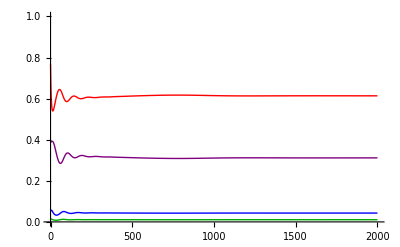

```mathematica
SEIRSPlot=Plot[{Sum[ssol[h,t],{h,1,2}],Sum[esol[h,p,c,t],{h,1,2},{p,1,2},{c,1,nE/.Pars}],Sum[isol[h,p,c,t],{h,1,2},{p,1,2},{c,1,nI/.Pars}],Sum[rsol[h,c,t],{h,1,2},{c,1,nR/.Pars}]},{t,0,tmax/.Pars},PlotRange->{0,1},PlotStyle->{{Red,Thick},{Darker[Green],Thick},{Blue,Thick},{Purple,Thick}}]
```

Here susceptible hosts are shown in red, exposed in green, infected in blue, and recovered in purple.

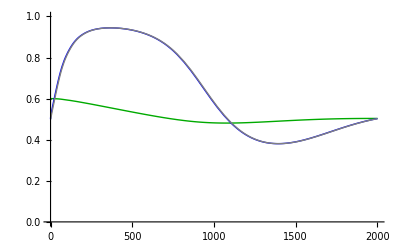

```mathematica
SEIRSPlot=Plot[{(1/Sum[(ssol[h,t]+Sum[esol[h,p,c,t],{p,1,2},{c,1,nE/.Pars}]+Sum[isol[h,p,c,t],{p,1,2},{c,1,nI/.Pars}]+Sum[rsol[h,c,t],{c,1,nR/.Pars}]),{h,1,2}])(ssol[1,t]+Sum[esol[1,p,c,t],{p,1,2},{c,1,nE/.Pars}]+Sum[isol[1,p,c,t],{p,1,2},{c,1,nI/.Pars}]+Sum[rsol[1,c,t],{c,1,nR/.Pars}]),Sum[esol[h,1,c,t],{h,1,2},{c,1,nE/.Pars}]/Sum[esol[h,p,c,t],{h,1,2},{p,1,2},{c,1,nE/.Pars}],Sum[isol[h,1,c,t],{h,1,2},{c,1,nI/.Pars}]/Sum[isol[h,p,c,t],{h,1,2},{p,1,2},{c,1,nI/.Pars}]},{t,0,tmax/.Pars},PlotRange->{0,1},PlotStyle->{{Darker[Green],Thick},{Blue,Thick},{Gray,Thick},{Purple,Thick}},AxesStyle->Directive[Thick,Bold,Black]]
```